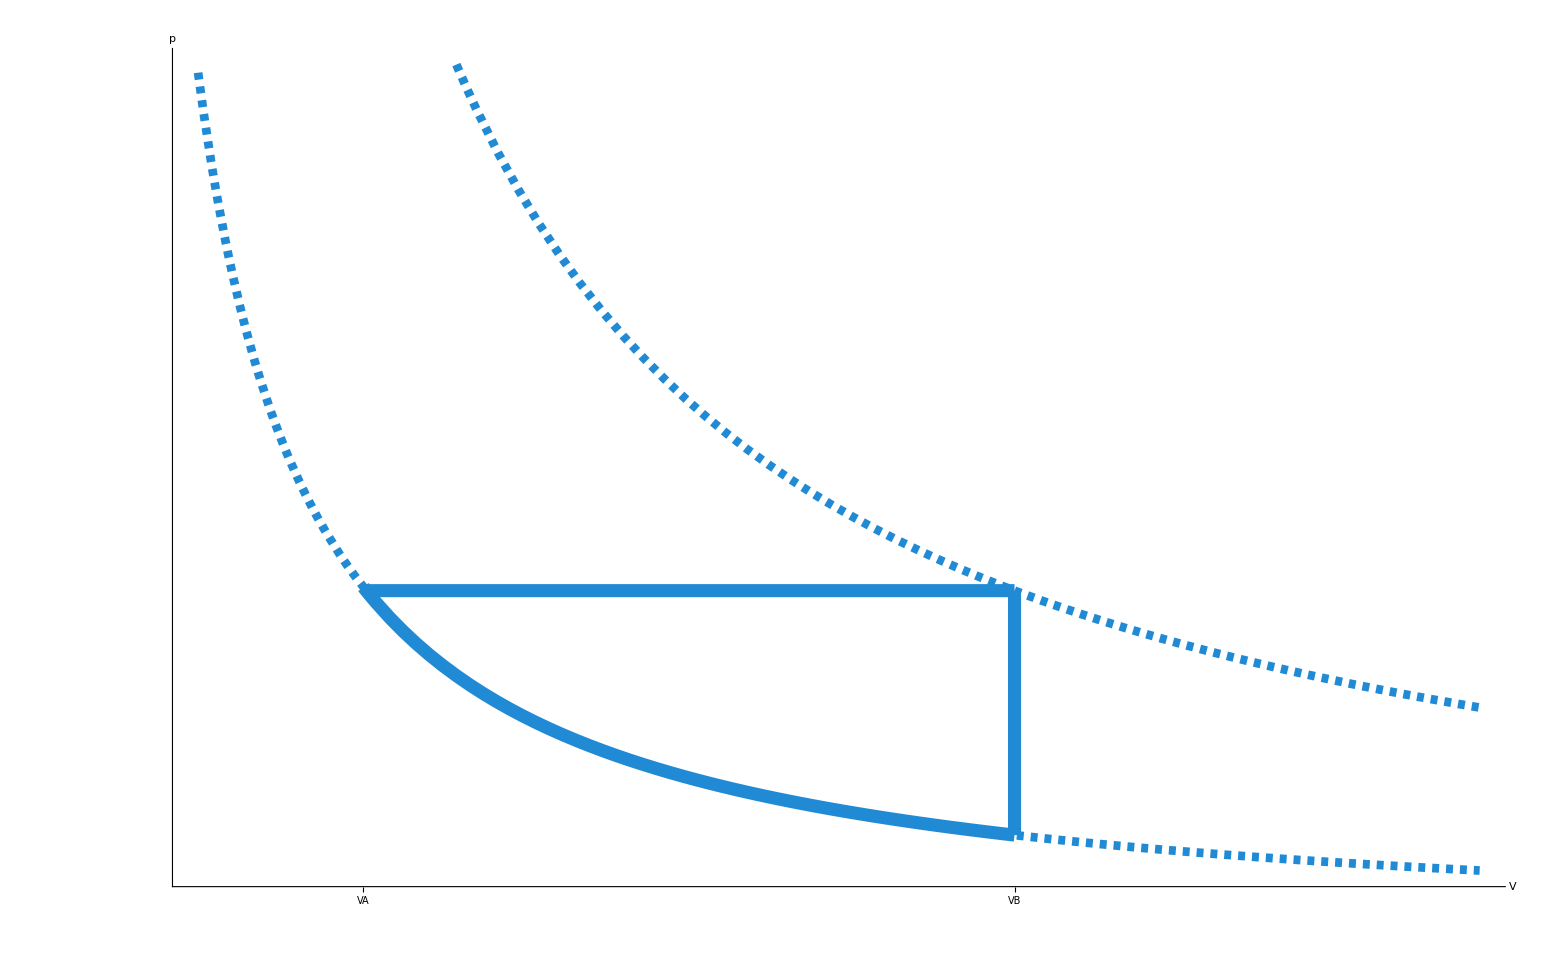

```mathematica
f[x_]:=1/x
g[x_]:=1/x
h[x_]:=3.3
i[x_]:=3.3/x
Show[{Plot[f[x],{x,0.3,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,0,1.5},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[i[x],{x,0.4,1.5},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[h[x],{x,0.3,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick, Epilog->{Thickness[0.006],RGBColor["#218ad4"],Line[{{1,1},{1,3.3}}]},Ticks->{{{0.3,VA},{1,VB}}, None},ImageSize->2000]
```

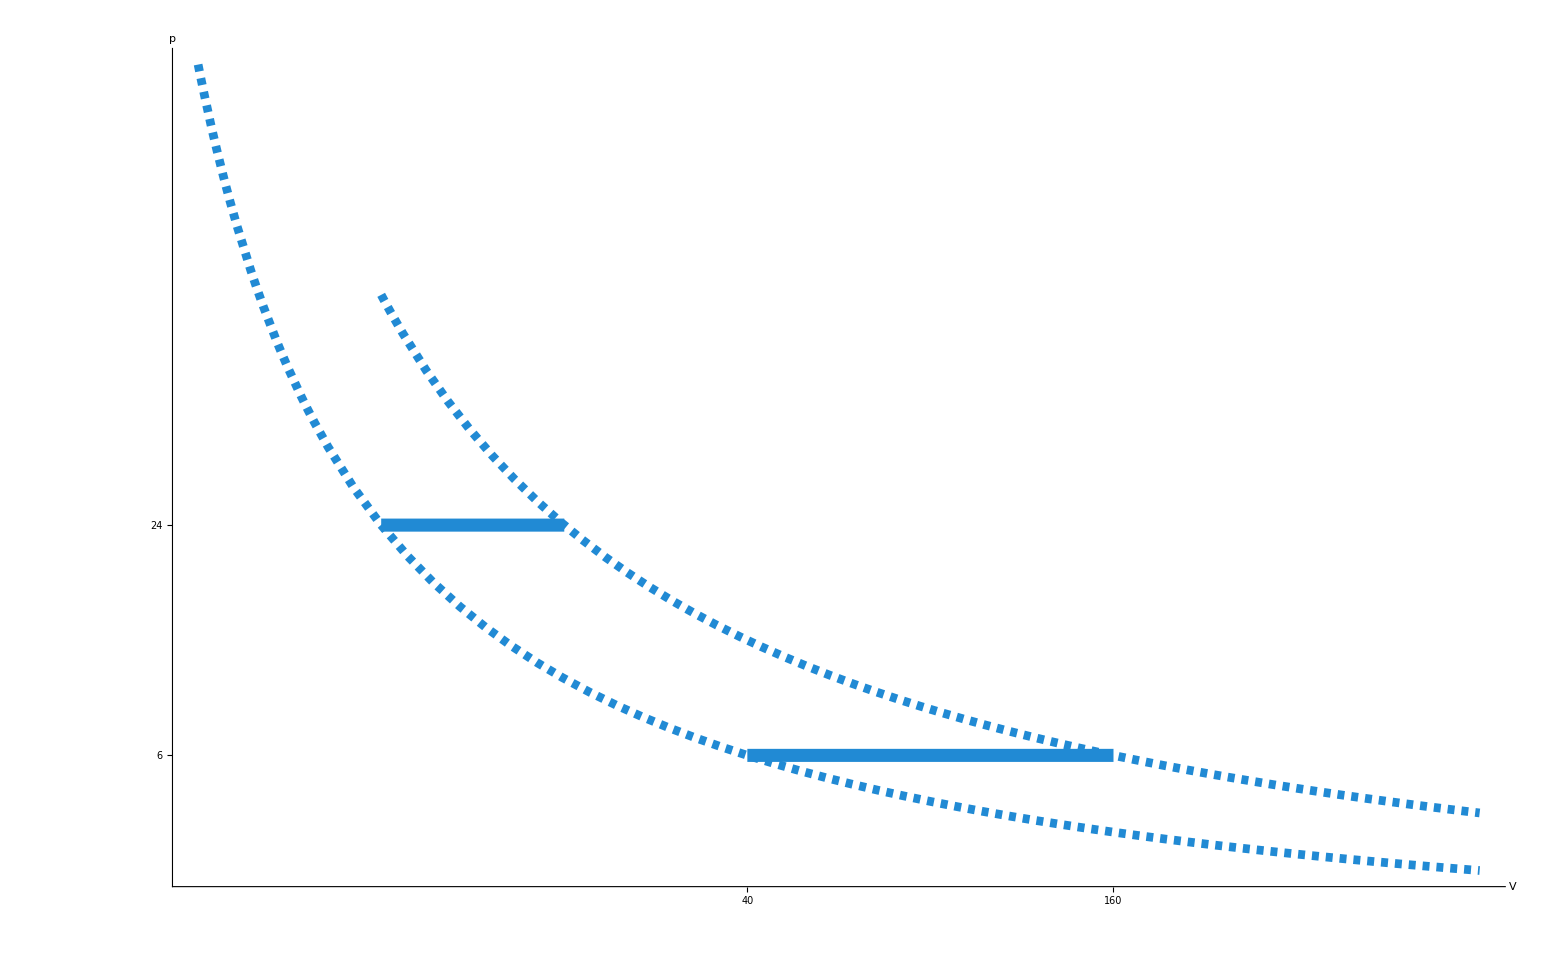

```mathematica
g[x_]:=1/x
h[x_]:=5
i[x_]:=1.5/x
j[x_]:=10
Show[{Plot[g[x],{x,0.05,0.4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[j[x],{x,0.1,0.15},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[i[x],{x,0.1,0.4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[h[x],{x,0.2,0.3},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick,Ticks->{{{0.2,40},{0.3,160}}, {{5,6},{10,24}}},ImageSize->2000]
```